In this model, I assume that there is a baseline rate of Th1 and Th2 proliferation, specified by the parameter b_i. I assume that self-promotion follows a Hill function with an exponent of 2, as this generates switch-like behavior. This assumption has some support from other models - for example, transcription factor self-promotion (and cross-inhibition) allows has switch-like behavior. I assume that the opposite Th cell population inhibits proliferation, rather than including the opposite as a negative term, which would biologically be interpreted as increasing the loss rate of the opposite Th cell population. And I assume a baseline loss rate of Th cells. These assumptions lead to the following model.

```mathematica
dTh1=b1+(s1 Th1^2)/(S1^2+Th1^2) I12/(I12+Th2) -m Th1;
dTh2=b2+(s2 Th2^2)/(S2^2+Th2^2) I21/(I21+Th1)-m Th2;
```

Because I don’t have a good sense of what the parameters of this model should be, I will nondimensionalize it.

```mathematica
dth1=Expand[that/TH1hat(dTh1/.{Th1->TH1hat th1,Th2->TH2hat th2})/.{TH1hat->S1,TH2hat->S2,that->1/m}/.b1->β1 m S1/.s1->σ1 m S1/.I12->ι12 S2]//Simplify
dth2=Expand[that/TH2hat(dTh2/.{Th1->TH1hat th1,Th2->TH2hat th2})/.{TH1hat->S1,TH2hat->S2,that->1/m}/.b2->β2 m S2/.s2->σ2 m S2/.I21->ι21 S1]//Simplify
```

-th1+β1+(th1^2 ι12 σ1)/((1+th1^2) (th2+ι12))

-th2+β2+(th2^2 ι21 σ2)/((1+th2^2) (th1+ι21))

This is more interpretable. For simplicity, let’s assume that the parameters are balanced between the Th cell populations, so there is no intrinsic bias towards either a Th1 or Th2 response. 

The parameter β_i=b_i/(m S_i) is the baseline immune supply rate divided by the rate that immune cells are depleted when at half the density that promotes maximal immune proliferation. The parameter σ_i=s_i/(m S_i) is the maximum immune proliferation rate divided by the same rate. Thus, rather than worrying excessively about the absolute values of these parameters, the more important thing is their relative value, with needing σ_i>>β_i since self-stimulated immune proliferation should be much higher than baseline immune supply. 

The parameter ι_ij=i_ij/I_ij is the ratio of the minimum inhibition of Th_j cells on Th_i proliferation to the number of Th_j cells where inhibition is half is maximal value (of 0). Thus this parameter must be less than 1 (if the minimum inhibition is greater than 1, Th_j cells actually fuel Th_i proliferation). 

η_i=S_i/I_ji gives the ratio of the half-maxima for self-stimulated proliferation by Th_i to cross-inhibition by Th_i on Th_j. This should also presumably be less than 1, reflecting that self-promotion is greater than cross-inhibition.

The form of the isoclines can give good insight into the possible dynamics of the system.

```mathematica
th1isocline=Solve[dth1==0,th2]//Simplify
th2isocline=Solve[dth2==0,th1]//Simplify
```

{{th2→(ι12 (-th1-th1^3+β1+th1^2 (β1+σ1)))/((1+th1^2) (th1-β1))}}

{{th1→(ι21 (-th2-th2^3+β2+th2^2 (β2+σ2)))/((1+th2^2) (th2-β2))}}

Note that the lines th1=0 and th2=0 are not isoclines for this system because of baseline Th cell-independent proliferation.  This is important because it means that only the intersections of the two lines above are possible equilibria of the system. In order to have multi-stability, the isoclines must cross at multiple places. This will be most easily facilitated by the slope of the isoclines changing signs.

Taking the derivatives of the isoclines with respect to the Th cell populations, you can see that the baseline immune supply parameters β_i are critical in determining the shape of the isocline.

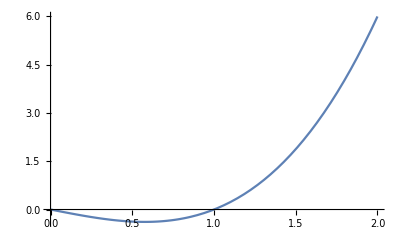

```mathematica
Plot[x^3-x,{x,0,2}]
```

```mathematica
Simplify[D[th1isocline[[1,1,2]],th1]]
Simplify[D[th2isocline[[1,1,2]],th2]]
```

-(th1 (-th1+th1^3+2 β1) ι12 σ1)/((1+th1^2)^2 (th1-β1)^2)

-(th2 (-th2+th2^3+2 β2) ι21 σ2)/((1+th2^2)^2 (th2-β2)^2)

Numerically solving for the zeros of these isoclines, you can see that the slope of the isoclines will only change signs if β_i is quite small, in which case there are multiple zeros, indicating that the isocline changes direction multiple times. If β_i is large, however, there are no zeros in the positive real plane, indicating that the slope will have a constant sign, which will limit the opportunities for multi-stability, as the most likely scenario is that the isoclines will cross only at a single point. 

This actually makes sense biologically: if the baseline immune supply rate is high, that makes polarization unlikely as the system will constantly be stimulating the proliferation of both Th cell subpopulations.

```mathematica
Table[N[Solve[(th1-th1^3-2 β1)==0,th1]],{β1,0,0.25,0.05}]
```

{{{th1→-1.},{th1→0.},{th1→1.}},{{th1→-1.04668},{th1→0.101031},{th1→0.945649}},{{th1→-1.08803},{th1→0.209149},{th1→0.878885}},{{th1→-1.12542},{th1→0.338936},{th1→0.786483}},{{th1→-1.1597},{th1→0.579852-0.0932014 ⅈ},{th1→0.579852+0.0932014 ⅈ}},{{th1→-1.19149},{th1→0.595744-0.254426 ⅈ},{th1→0.595744+0.254426 ⅈ}}}

```mathematica
N[Sqrt[3/81]]
```

0.19245

```mathematica
N[Simplify[Solve[th1-th1^3-2 β1==0,th1]]]
```

{{th1→-(0.48075 (1.44225+(9. β1+√(-3.+81. β1^2))^(2/3)))/((9. β1+√(-3.+81. β1^2))^(1/3))},{th1→(0.240375 ((1.44225+2.49805 ⅈ)+(1.-1.73205 ⅈ) (9. β1+√(-3.+81. β1^2))^(2/3)))/((9. β1+√(-3.+81. β1^2))^(1/3))},{th1→(0.240375 ((1.44225-2.49805 ⅈ)+(1.+1.73205 ⅈ) (9. β1+√(-3.+81. β1^2))^(2/3)))/((9. β1+√(-3.+81. β1^2))^(1/3))}}

Here are a set of parameters that show the most multi-stability that is possible in this system. The filled black circles show the stable equilibria, and the open circles show the unstable equilibria. You can see that there 4 stable equilibria, corresponding to a low (but balanced) co-expression equilibrium, a high Th1/Th2 co-expression equilibrium, and the two polarized equilibria.

{{th1→0.167811,th2→1.45729},{th1→0.180241,th2→0.446222},{th1→0.184947,th2→0.184947},{th1→0.446222,th2→0.180241},{th1→0.494769,th2→0.494769},{th1→0.678821,th2→1.28958},{th1→1.12255,th2→1.12255},{th1→1.28958,th2→0.678821},{th1→1.45729,th2→0.167811}}

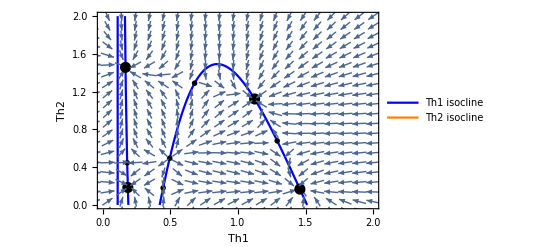

```mathematica
params={σ1->2,σ2->2,β1->0.12,β2->0.12,ι12->10,ι21->10};
eq=N[Solve[{dth1==0,dth2==0}/.params,{th1,th2}]];
realEq=eq⟦Flatten[Intersection[Position[eq⟦;;,1,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)],
Position[eq⟦;;,2,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)]]]⟧
(* stable equilibria have a positive determinant and a negative trace *)
stableInds=Intersection[Flatten[Position[Det[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x>0]],
Flatten[Position[Tr[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x<0]]];
unstableInds=Complement[Table[i,{i,1,Length[realEq]}],stableInds];
Show[ListLinePlot[Table[{th1,th1isocline⟦1,1,2⟧/.params},{th1,0.1,20,0.01}],PlotRange->{{0,2},{0,2}},PlotStyle->{Thick,Blue},PlotLegends->LineLegend[{Blue,Orange},{"Th1 isocline","Th2 isocline"}]],
ListLinePlot[Table[{th2isocline⟦1,1,2⟧/.params,th2},{th2,0.1,20,0.01}],PlotStyle->{Thick,Orange}],
ListPlot[realEq⟦stableInds,;;,2⟧,PlotStyle->{Black,PointSize[0.02]}],
ListPlot[realEq⟦unstableInds,;;,2⟧,PlotMarkers->"OpenMarkers",PlotStyle->{Black}],
VectorPlot[{dth1/.params,dth2/.params},{th1,-1,2},{th2,-1,2},VectorScale->{0.025,0.9,None},VectorColorFunction->None, VectorStyle->Gray[0.8],VectorPoints->30],
Frame->True,
FrameLabel->{"Th1","Th2"}
]
```

If you weaken the baseline response, you lose the high co-expression equilibrium, and end up with only three stable equilibria representing low co-expression or polarization.

{{th1→0.0960798,th2→1.37689},{th1→0.0979588,th2→0.585035},{th1→0.0993591,th2→0.0993591},{th1→0.585035,th2→0.0979588},{th1→0.752926,th2→0.752926},{th1→0.914991,th2→0.914991},{th1→1.37689,th2→0.0960798}}

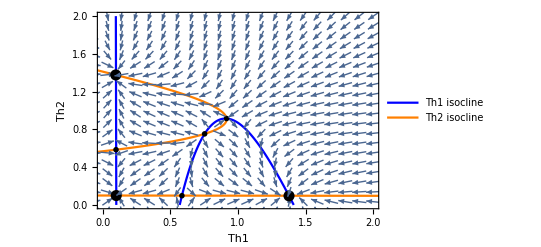

```mathematica
params={σ1->2,σ2->2,β1->0.08,β2->0.08,ι12->10,ι21->10};
eq=N[Solve[{dth1==0,dth2==0}/.params,{th1,th2}]];
realEq=eq⟦Flatten[Intersection[Position[eq⟦;;,1,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)],
Position[eq⟦;;,2,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)]]]⟧
(* stable equilibria have a positive determinant and a negative trace *)
stableInds=Intersection[Flatten[Position[Det[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x>0]],
Flatten[Position[Tr[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x<0]]];
unstableInds=Complement[Table[i,{i,1,Length[realEq]}],stableInds];
Show[ListLinePlot[Table[{th1,th1isocline⟦1,1,2⟧/.params},{th1,0.01,20,0.01}],PlotRange->{{0,2},{0,2}},PlotStyle->{Thick,Blue},PlotLegends->LineLegend[{Blue,Orange},{"Th1 isocline","Th2 isocline"}]],
ListLinePlot[Table[{th2isocline⟦1,1,2⟧/.params,th2},{th2,0.01,20,0.01}],PlotStyle->{Thick,Orange}],
ListPlot[realEq⟦stableInds,;;,2⟧,PlotStyle->{Black,PointSize[0.02]}],
ListPlot[realEq⟦unstableInds,;;,2⟧,PlotMarkers->"OpenMarkers",PlotStyle->{Black}],
VectorPlot[{dth1/.params,dth2/.params},{th1,-1,2},{th2,-1,2},VectorScale->{0.025,0.9,None},VectorColorFunction->None, VectorStyle->Gray[0.8],VectorPoints->30],
Frame->True,
FrameLabel->{"Th1","Th2"}
]
```

But if you strengthen the baseline immune response, you end up with three equilibria representing polarization and high co-expression. Any further strengthening and the only stable equilibrium is high co-expression.

{{th1→0.260646,th2→1.49875},{th1→0.49988,th2→1.4281},{th1→1.2102,th2→1.2102},{th1→1.4281,th2→0.49988},{th1→1.49875,th2→0.260646}}

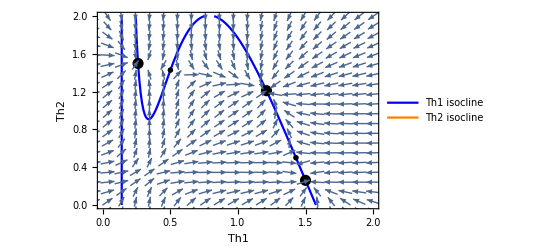

```mathematica
params={σ1->2,σ2->2,β1->0.15,β2->0.15,ι12->10,ι21->10};
eq=N[Solve[{dth1==0,dth2==0}/.params,{th1,th2}]];
realEq=eq⟦Flatten[Intersection[Position[eq⟦;;,1,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)],
Position[eq⟦;;,2,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)]]]⟧
(* stable equilibria have a positive determinant and a negative trace *)
stableInds=Intersection[Flatten[Position[Det[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x>0]],
Flatten[Position[Tr[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x<0]]];
unstableInds=Complement[Table[i,{i,1,Length[realEq]}],stableInds];
Show[ListLinePlot[Table[{th1,th1isocline⟦1,1,2⟧/.params},{th1,0.01,20,0.01}],PlotRange->{{0,2},{0,2}},PlotStyle->{Thick,Blue},PlotLegends->LineLegend[{Blue,Orange},{"Th1 isocline","Th2 isocline"}]],
ListLinePlot[Table[{th2isocline⟦1,1,2⟧/.params,th2},{th2,0.01,20,0.01}],PlotStyle->{Thick,Orange}],
ListPlot[realEq⟦stableInds,;;,2⟧,PlotStyle->{Black,PointSize[0.02]}],
ListPlot[realEq⟦unstableInds,;;,2⟧,PlotMarkers->"OpenMarkers",PlotStyle->{Black}],
VectorPlot[{dth1/.params,dth2/.params},{th1,-1,2},{th2,-1,2},VectorScale->{0.025,0.9,None},VectorColorFunction->None, VectorStyle->Gray[0.8],VectorPoints->30],
Frame->True,
FrameLabel->{"Th1","Th2"}
]
```

Strengthening cross-inhibition:

{{th1→0.160669,th2→1.42531},{th1→0.175447,th2→0.462892},{th1→0.18268,th2→0.18268},{th1→0.462892,th2→0.175447},{th1→0.588251,th2→0.588251},{th1→0.88865,th2→0.88865},{th1→1.42531,th2→0.160669}}

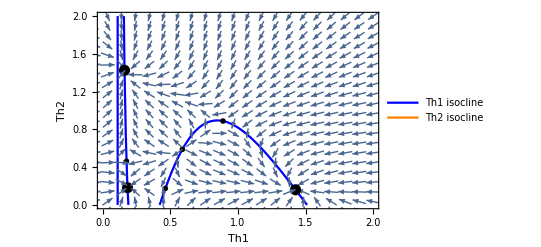

```mathematica
params={σ1->2,σ2->2,β1->0.12,β2->0.12,ι12->6,ι21->6};
eq=N[Solve[{dth1==0,dth2==0}/.params,{th1,th2}]];
realEq=eq⟦Flatten[Intersection[Position[eq⟦;;,1,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)],
Position[eq⟦;;,2,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)]]]⟧
(* stable equilibria have a positive determinant and a negative trace *)
stableInds=Intersection[Flatten[Position[Det[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x>0]],
Flatten[Position[Tr[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x<0]]];
unstableInds=Complement[Table[i,{i,1,Length[realEq]}],stableInds];
Show[ListLinePlot[Table[{th1,th1isocline⟦1,1,2⟧/.params},{th1,0.1,20,0.01}],PlotRange->{{0,2},{0,2}},PlotStyle->{Thick,Blue},PlotLegends->LineLegend[{Blue,Orange},{"Th1 isocline","Th2 isocline"}]],
ListLinePlot[Table[{th2isocline⟦1,1,2⟧/.params,th2},{th2,0.1,20,0.01}],PlotStyle->{Thick,Orange}],
ListPlot[realEq⟦stableInds,;;,2⟧,PlotStyle->{Black,PointSize[0.02]}],
ListPlot[realEq⟦unstableInds,;;,2⟧,PlotMarkers->"OpenMarkers",PlotStyle->{Black}],
VectorPlot[{dth1/.params,dth2/.params},{th1,-1,2},{th2,-1,2},VectorScale->{0.025,0.9,None},VectorColorFunction->None, VectorStyle->Gray[0.8],VectorPoints->30],
Frame->True,
FrameLabel->{"Th1","Th2"}
]
```

Strengthening cross-inhibition:

{{th1→0.172799,th2→1.47405},{th1→0.18291,th2→0.437772},{th1→0.186186,th2→0.186186},{th1→0.437772,th2→0.18291},{th1→0.465626,th2→0.465626},{th1→0.575729,th2→1.38783},{th1→1.2381,th2→1.2381},{th1→1.38783,th2→0.575729},{th1→1.47405,th2→0.172799}}

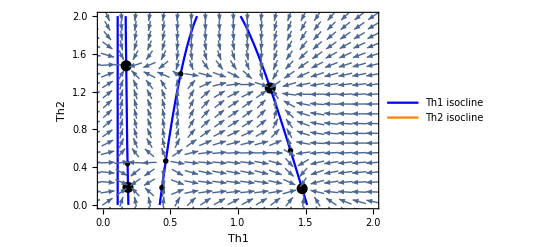

```mathematica
params={σ1->2,σ2->2,β1->0.12,β2->0.12,ι12->15,ι21->15};
eq=N[Solve[{dth1==0,dth2==0}/.params,{th1,th2}]];
realEq=eq⟦Flatten[Intersection[Position[eq⟦;;,1,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)],
Position[eq⟦;;,2,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)]]]⟧
(* stable equilibria have a positive determinant and a negative trace *)
stableInds=Intersection[Flatten[Position[Det[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x>0]],
Flatten[Position[Tr[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x<0]]];
unstableInds=Complement[Table[i,{i,1,Length[realEq]}],stableInds];
Show[ListLinePlot[Table[{th1,th1isocline⟦1,1,2⟧/.params},{th1,0.1,20,0.01}],PlotRange->{{0,2},{0,2}},PlotStyle->{Thick,Blue},PlotLegends->LineLegend[{Blue,Orange},{"Th1 isocline","Th2 isocline"}]],
ListLinePlot[Table[{th2isocline⟦1,1,2⟧/.params,th2},{th2,0.1,20,0.01}],PlotStyle->{Thick,Orange}],
ListPlot[realEq⟦stableInds,;;,2⟧,PlotStyle->{Black,PointSize[0.02]}],
ListPlot[realEq⟦unstableInds,;;,2⟧,PlotMarkers->"OpenMarkers",PlotStyle->{Black}],
VectorPlot[{dth1/.params,dth2/.params},{th1,-1,2},{th2,-1,2},VectorScale->{0.025,0.9,None},VectorColorFunction->None, VectorStyle->Gray[0.8],VectorPoints->30],
Frame->True,
FrameLabel->{"Th1","Th2"}
]
```

Strengthening self-promotion:

{{th1→0.197032,th2→2.12833},{th1→0.373799,th2→2.07608},{th1→1.71132,th2→1.71132},{th1→2.07608,th2→0.373799},{th1→2.12833,th2→0.197032}}

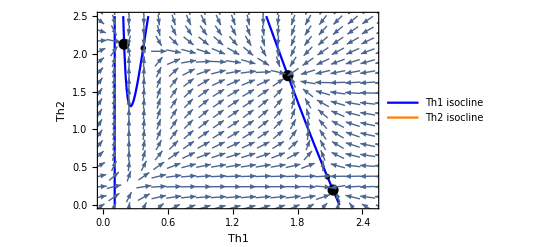

```mathematica
params={σ1->2.5,σ2->2.5,β1->0.12,β2->0.12,ι12->10,ι21->10};
eq=N[Solve[{dth1==0,dth2==0}/.params,{th1,th2}]];
realEq=eq⟦Flatten[Intersection[Position[eq⟦;;,1,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)],
Position[eq⟦;;,2,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)]]]⟧
(* stable equilibria have a positive determinant and a negative trace *)
stableInds=Intersection[Flatten[Position[Det[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x>0]],
Flatten[Position[Tr[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x<0]]];
unstableInds=Complement[Table[i,{i,1,Length[realEq]}],stableInds];
Show[ListLinePlot[Table[{th1,th1isocline⟦1,1,2⟧/.params},{th1,0.1,20,0.01}],PlotRange->{{0,2.5},{0,2.5}},PlotStyle->{Thick,Blue},PlotLegends->LineLegend[{Blue,Orange},{"Th1 isocline","Th2 isocline"}]],
ListLinePlot[Table[{th2isocline⟦1,1,2⟧/.params,th2},{th2,0.1,20,0.01}],PlotStyle->{Thick,Orange}],
ListPlot[realEq⟦stableInds,;;,2⟧,PlotStyle->{Black,PointSize[0.02]}],
ListPlot[realEq⟦unstableInds,;;,2⟧,PlotMarkers->"OpenMarkers",PlotStyle->{Black}],
VectorPlot[{dth1/.params,dth2/.params},{th1,-1,3},{th2,-1,3},VectorScale->{0.025,0.9,None},VectorColorFunction->None, VectorStyle->Gray[0.8],VectorPoints->30],
Frame->True,
FrameLabel->{"Th1","Th2"}
]
```

{{th1→0.161368,th2→1.04283},{th1→0.164297,th2→0.680422},{th1→0.169345,th2→0.169345},{th1→0.680422,th2→0.164297},{th1→1.04283,th2→0.161368}}

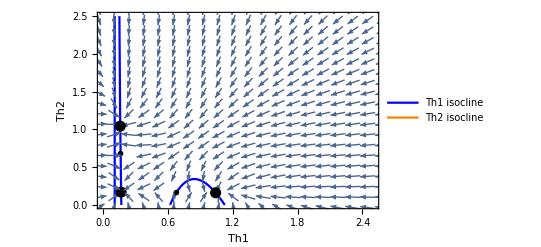

```mathematica
params={σ1->1.8,σ2->1.8,β1->0.12,β2->0.12,ι12->10,ι21->10};
eq=N[Solve[{dth1==0,dth2==0}/.params,{th1,th2}]];
realEq=eq⟦Flatten[Intersection[Position[eq⟦;;,1,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)],
Position[eq⟦;;,2,2⟧,x_/;(Abs[Im[x]]<10^-6&&Re[x]>0)]]]⟧
(* stable equilibria have a positive determinant and a negative trace *)
stableInds=Intersection[Flatten[Position[Det[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x>0]],
Flatten[Position[Tr[D[{dth1,dth2},{{th1,th2}}]]/.params/.realEq,x_/;x<0]]];
unstableInds=Complement[Table[i,{i,1,Length[realEq]}],stableInds];
Show[ListLinePlot[Table[{th1,th1isocline⟦1,1,2⟧/.params},{th1,0.1,20,0.01}],PlotRange->{{0,2.5},{0,2.5}},PlotStyle->{Thick,Blue},PlotLegends->LineLegend[{Blue,Orange},{"Th1 isocline","Th2 isocline"}]],
ListLinePlot[Table[{th2isocline⟦1,1,2⟧/.params,th2},{th2,0.1,20,0.01}],PlotStyle->{Thick,Orange}],
ListPlot[realEq⟦stableInds,;;,2⟧,PlotStyle->{Black,PointSize[0.02]}],
ListPlot[realEq⟦unstableInds,;;,2⟧,PlotMarkers->"OpenMarkers",PlotStyle->{Black}],
VectorPlot[{dth1/.params,dth2/.params},{th1,-1,3},{th2,-1,3},VectorScale->{0.025,0.9,None},VectorColorFunction->None, VectorStyle->Gray[0.8],VectorPoints->30],
Frame->True,
FrameLabel->{"Th1","Th2"}
]
```

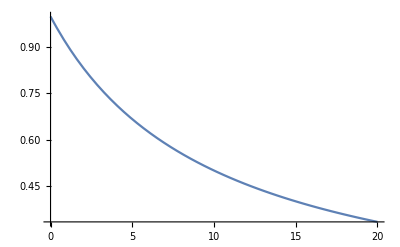

```mathematica
Plot[10/(10+x),{x,0,20}]
```